```mathematica
LaunchKernels[16]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

```mathematica
Get["~/work/ambit-stochastics/mathematica/SpectralDensityEstimation.m"]
Get["~/work/ambit-stochastics/mathematica/Utilities.m"]
```

```mathematica
NumberVectorQ[x_]:=VectorQ[x,NumberQ];
```

## BSS processes

```mathematica
Clear[PrepareStepKernel]

PrepareStepKernel[kernel_,delta_,n_]:=
Module[
{G,G0,G1},
G=Table[kernel[(j+0.5)*delta],{j,0,n-1}];
G0=delta*G;
G1=Sqrt[delta]*G;
{G0,G1}
];
```

```mathematica
Clear[PrepareKernel]

PrepareKernel[kernel_,delta_,n_,0]:=
Module[
{G10,G20},
G10=Table[delta NIntegrate[kernel[(j+u)delta],{u,0,1}],{j,0,n-1}];
G20=Sqrt@Table[delta NIntegrate[kernel[(j+u)delta]^2,{u,0,1}],{j,0,n-1}];
{{G10},{G20}}
];

PrepareKernel[kernel_,delta_,n_,1]:=
Module[
{G10,G11,G20,G21},
G10=Table[delta NIntegrate[kernel[(j+u)delta]u,{u,0,1}],{j,0,n-1}];
G11=Table[delta NIntegrate[kernel[(j+u)delta](1-u),{u,0,1}],{j,0,n-1}];
G20=Sqrt@Table[delta NIntegrate[kernel[(j+u)delta]^2u,{u,0,1}],{j,0,n-1}];
G21=Sqrt@Table[delta NIntegrate[kernel[(j+u)delta]^2(1-u),{u,0,1}],{j,0,n-1}];
{{G10,G11},{G20,G21}}
];
```

```mathematica
Clear[BSSSimulateDeterministicIntegral,BSSSimulateStochasticIntegral]

BSSSimulateDeterministicIntegral[G0_?NumberVectorQ,sigma_]:=
ListConvolve[G0,sigma^2];

BSSSimulateDeterministicIntegral[{G10_?NumberVectorQ},sigma_]:=
ListConvolve[G10,sigma^2];

BSSSimulateDeterministicIntegral[{G10_?NumberVectorQ,G11_?NumberVectorQ},sigma_]:=
ListConvolve[G10,Most[sigma]^2]+ListConvolve[G11,Rest[sigma]^2];

BSSSimulateStochasticIntegral[G1_?NumberVectorQ,sigma_]:=
Module[{U0},
Print["0"];
U0=RandomVariate[NormalDistribution[],{Length[sigma]}];
ListConvolve[G1,sigma*U0]
];

BSSSimulateStochasticIntegral[{G20_?NumberVectorQ},sigma_]:=
Module[{U0},
Print["1"];
U0=RandomVariate[NormalDistribution[],{Length[sigma]}];
ListConvolve[G20,sigma*U0]
];

BSSSimulateStochasticIntegral[{G20_?NumberVectorQ,G21_?NumberVectorQ},sigma_]:=
Module[{U0,U1},
Print["2"];
U0=RandomVariate[NormalDistribution[],{Length[sigma]-1}];
U1=RandomVariate[NormalDistribution[],{Length[sigma]-1}];
ListConvolve[G20,Most[sigma]*U0]+ListConvolve[G21,Rest[sigma]*U1]
];
```

## Trawl processes

```mathematica
Clear[GaussianSeed,NormalInverseGaussianSeed,GeneralisedHyperbolicSeed]

GaussianSeed[mean_,variance_][volume_]:=
NormalDistribution[mean*volume,Sqrt[variance*volume]];

NormalInverseGaussianSeed[alpha_,beta_,mu_,delta_][volume_]:=
GeneralisedHyperbolicSeed[-1/2,alpha,beta,mu,delta][volume];

GeneralisedHyperbolicSeed[lambda_,alpha_,beta_,mu_,delta_][volume_]:=
HyperbolicDistribution[lambda,alpha,beta,delta*volume,mu*volume];
```

```mathematica
Clear[PrepareTrawlVolumes,ParallelPrepareTrawlVolumes]

PrepareTrawlVolumes[kernel_,upperBound_,n_]:=
Append[Most@#-Rest@#,Last@#]&@Table[2.0*NIntegrate[kernel[s],{s,(i-1)*upperBound/n,i*upperBound/n}],{i,n}];

ParallelPrepareTrawlVolumes[kernel_,upperBound_,n_]:=
Append[Most@#-Rest@#,Last@#]&@ParallelTable[2.0*NIntegrate[kernel[s],{s,(i-1)*upperBound/n,i*upperBound/n}],{i,n}];
```

```mathematica
Clear[MovingTotalC]

MovingTotalC=
Compile[{{x,_Real,1},{n,_Integer,0}},
With[{y=Prepend[Accumulate[x],0.0]},Drop[y,n]-Drop[y,-n]],
CompilationTarget->"C"
];

Clear[SimulateTrawlProcess]

SimulateTrawlProcess[volumes_,seed_,n_]:=
SimulateTrawlProcess[volumes,seed,n,Range@Length@volumes];

SimulateTrawlProcess[volumes_,seed_,n_,counts_]:=
Fold[
#1+MovingTotalC[RandomVariate[seed[#2⟦1⟧],n+#2⟦2⟧-1],#2⟦2⟧]&,
ConstantArray[0.0,n],
Transpose@{volumes,counts}
];

Clear[ParallelSimulateTrawlProcess]

ParallelSimulateTrawlProcess[volumes_,seed_,n_]:=
ParallelCombine[
SimulateTrawlProcess[#⟦All,1⟧,seed,n,#⟦All,2⟧]&,
Transpose@{volumes,Range@Length@volumes},
Total[{##}]&
];
```

## Examples of use

```mathematica
g1[t_,nu_,lambda_]:=lambda^nu/Gamma[nu]*t^(nu-1)*Exp[-lambda*t];
```

```mathematica
nu1=5/6;
lambda1=1.0;
delta1=0.01;
n1=Ceiling[10/(lambda1*delta1)];
Gstep=PrepareStepKernel[g1[#,nu1,lambda1]&,delta1,n1];
G0=PrepareKernel[g1[#,nu1,lambda1]&,delta1,n1,0];
G1=PrepareKernel[g1[#,nu1,lambda1]&,delta1,n1,1];
s1=Table[1.0,{10^6}];
```

```mathematica
ystep=BSSSimulateStochasticIntegral[Gstep[[2]],s1];
y0=BSSSimulateStochasticIntegral[G0[[2]],s1];y1=BSSSimulateStochasticIntegral[G1[[2]],s1];
```

0

1

2

```mathematica
k=1;
sdfstep=AdjoinFrequencies@WOSASpectralDensityEstimate[ystep[[;;;;k]],k delta1,HanningTaper,10000,0.0];
sdf0=AdjoinFrequencies@WOSASpectralDensityEstimate[y0[[;;;;k]],k delta1,HanningTaper,10000,0.0];sdf1=AdjoinFrequencies@WOSASpectralDensityEstimate[y1[[;;;;k]],k delta1,HanningTaper,10000,0.0];
```

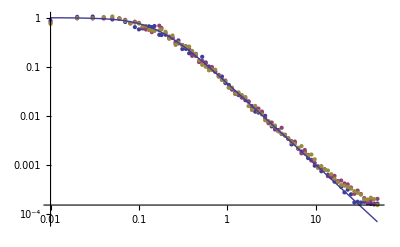

```mathematica
Show[
ListLogLogPlot[
{
LogTake[sdfstep,100],
LogTake[sdf0,100],
LogTake[sdf1,100]
},PlotRange->All
],
LogLogPlot[(1+((2π ω)/lambda1)^2)^-nu1,{ω,sdf0[[1,1]],sdf0[[-1,1]]},PlotRange->All],
PlotRange->All
]
```

```mathematica
corFun[s_,ν_,λ_]:=(2^(3/2-ν) (s/λ)^(-1/2+ν) λ^(-1+2 ν) BesselK[-1/2+ν,s λ])/Gamma[-1/2+ν];
```

```mathematica
lag=IntegerLogScale[1,10000,100];
covstep=CorrelationFunction[ystep,{lag}];
cov0=CorrelationFunction[y0,{lag}];
cov1=CorrelationFunction[y1,{lag}];
```

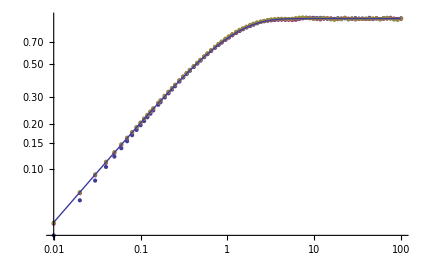

```mathematica
Show[
ListLogLogPlot[
{
Transpose@{delta1 lag,1-covstep},
Transpose@{delta1 lag,1-cov0},
Transpose@{delta1 lag,1-cov1}
},
PlotRange->All,
Joined->False
],
LogLogPlot[1-corFun[s,nu1,lambda1],{s,delta1 lag[[1]],delta1 lag[[-1]]},PlotRange->All]
]
```

```mathematica
SDF2[ω_,ν1_,ν2_,λ1_,λ2_]:=(1+((2π ω)/λ1)^2)^-ν1(1+((2π ω)/λ2)^2)^-ν2;
SetAttributes[cov2,Listable]
cov2[x_,ν1_,ν2_,λ1_,λ2_]:=2NIntegrate[SDF2[ω,ν1,ν2,λ1,λ2]Cos[2π x ω],{ω,0,∞},Method->If[x==0,Automatic,"LevinRule"]];
```

```mathematica
lag2={0.0}~Join~LogScale[0.0001,100,100];
tbl2=cov2[lag2,5/6,13/6,1,1000];//AbsoluteTiming
```

{5.98344,Null}

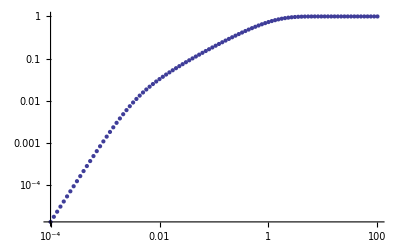

```mathematica
ListLogLogPlot[Transpose@{lag2,1-tbl2/tbl2[[1]]}]
```

```mathematica
Assuming[
0<λ&&ν1>1/2&&ν2>0&&x>0,
2Integrate[(1+ω^2)^-ν1(1+(ω/λ)^2)^-ν2 Cos[x ω],{ω,0,∞}]//FullSimplify
]
```

2 ∫_0^∞ (1+ω^2)^-ν1 (1+ω^2/λ^2)^-ν2 Cos[x ω]ⅆω

## Examples

```mathematica
Clear[trawlKernel1]
trawlKernel1[t_,T_,L_,theta_]:=
1/L((T^theta-t^theta)/((T/L)^theta+t^theta))^(1/theta);
```

```mathematica
vol1=ParallelPrepareTrawlVolumes[trawlKernel1[#,1,100,2]&,1,1000];//AbsoluteTiming
```

{0.4245,Null}

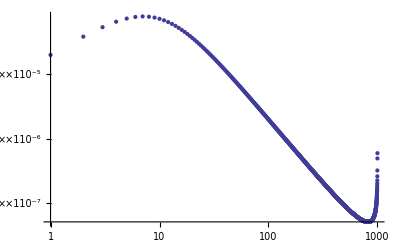

```mathematica
ListLogLogPlot[vol1,PlotRange->Full]
```

```mathematica
s1=ParallelSimulateTrawlProcess[vol1,GaussianSeed[-0.5,1.0],10^6];//AbsoluteTiming
```

{18.6524,Null}

```mathematica
y0=BSSSimulateStochasticIntegral[G0[[2]],Exp[s1]];//AbsoluteTiming
z0=BSSSimulateDeterministicIntegral[G0[[1]],Exp[s1]];//AbsoluteTiming
```

1

{0.20309,Null}

{0.05355,Null}

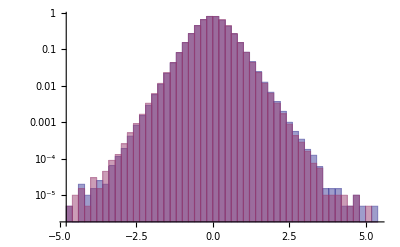

```mathematica
x0=y0+0.4z0;
Histogram[{Drop[x0,10]-Drop[x0,-10],Drop[y0,10]-Drop[y0,-10]},50,{"Log","PDF"}]
```